Analysis of the U.S. Government Foreign Assistance

Federico Dradi

Riccardo Di Virgilio

Most representative image

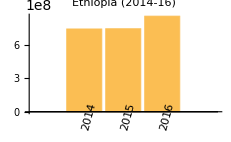
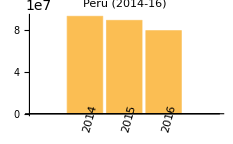

Mathematica notebook: ProjectWSS2017_Dradi2.nb

Abstract

GOAL OF THE PROJECT: 
We aim at analyzing data from the website “foreignassistance.gov” (U.S. government’s main tool for improving transparency in U.S. foreign assistance spending). In the range of years 2014-16 we want to study the U.S. foreign assistance investments of the government’s main agencies in several categories of a sample of countries. Moreover, we want to display how the investments are distributed in Peru, Jordan and Ethiopia.

SUMMARY OF WORK: 
After having imported data via the API, we have selected the important information by using the main functions for data analysis and data visualization, such as Association, Dataset, Select, Table, MapAt and ListLogPlot, PieChart and BarChart. Note that the last three functions were employed for displaying our results.

RESULTS AND FUTURE  WORK:  
In the first part of our analysis we have seen how investments of a given agency have been distributed through the different categories. This investigation has been done for all the countries of the studied sample and the results have been displayed via charts. In the second part of our analysis we have focused on Peru, Jordan and Ethiopia. We have showed how the investments in a specific category come from all the considered agencies in 2014-2016. Finally, we have compared the U.S. government’s different aid to Peru, Jordan and Ethiopia. An increase of the American financial support to Ethiopia in the last two years has been observed. On the contrary, a decrease of such a financial support to Jordan and Peru has been highlighted. Effective pie charts have showed how much of the total aid has been given to each category of these countries. Note that our codes have been written for being independent from the range of years under consideration.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

## Motivation for this analysis

The United States spends many billion on foreign assistance every year to improve health, support democracy and other categories, and achieve other U.S. foreign policy goals. Besides enabling stakeholders and the general public to better understand U.S. foreign assistance investments around the world, this analysis can be priceless to project implementers and managers to effectively manage these funds.

## Comparison in U.S. foreign assistance spending (Figure 1) - Example

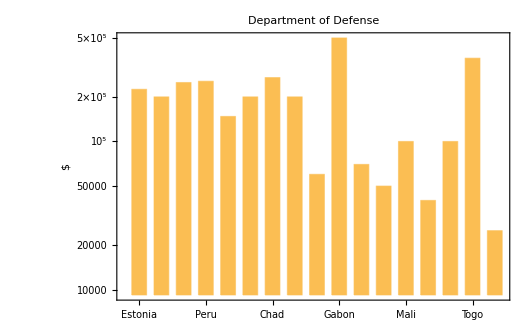
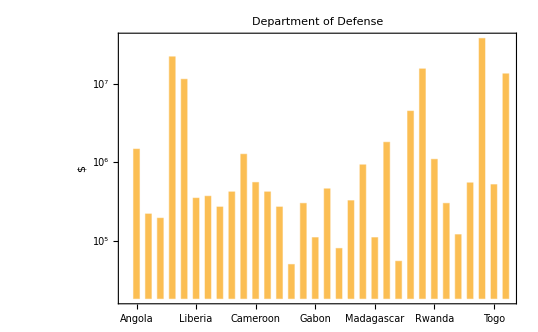
Year: 2015-2016, Category: Health, Agency: Department of Defense (=department of the federal executive branch entrusted with formulating military policies and maintaining American military forces)
-Graphics--Graphics-

Mathematica notebook: ProjectWSS2017_Dradi1.nb

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Details

## Comparison in U.S. foreign assistance spending (Figure 1) - Example

In Figure 7 we can see two charts that present grouped data with rectangular bars with lengths proportional to the values that they represent, i.e. the amount of money given to those countries which are on the x-axis. Specifically, both bar charts provide the distribution of the U.S. Government Foreign Assistance in the category “Health”. Here the agency “Department of Defense” has been taken into consideration.  This analysis has been performed for both 2015 and 2016. The comparison of these two charts shows  clearly a different investment on this particular category.

## Pie chart - Ethiopia 2016 - Peru 2016 (Figure 2)

Figure 2 shows two pie charts which represent how the U.S. Government Foreign Assistance has been distributed into the “categories” in 2016.  The pie chart for Ethiopia and Peru are respectively the pie chart on the left- and right-side of the figure. By comparing our results we can visualize immediately the different choices of investment  between Ethiopia and Peru. Note that this result takes into consideration the contribution of all the agencies.

Mathematica notebook: ProjectWSS2017_Dradi2.nb

## ListLogPlot - Ethiopia - Peru (Figure 3)

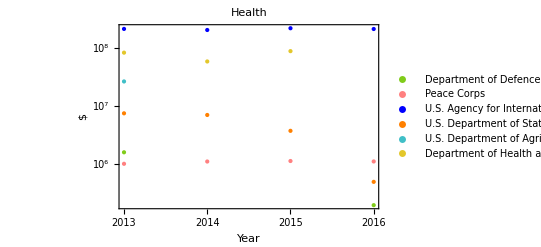
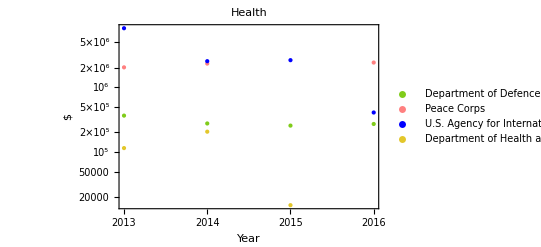

Figure 3 displays the U.S. Government Foreign Assistance on the category “Health” coming from several agencies in the range of years 2013-2016. In particular, the chart on the left-side is for Ethiopia and the chart on the right-side is for Peru. The comparison between these charts gives us the time evolution of such an aid to Ethiopia and Peru.

Mathematica notebook: ProjectWSS2017_Dradi3.nb

## Bar chart - Total money donated - Jordan - Ethiopia - Peru (2014-16) (Figure 4)

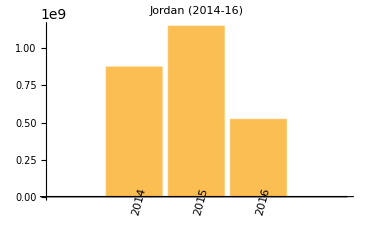
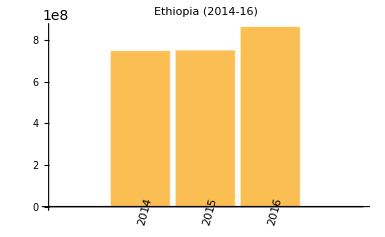
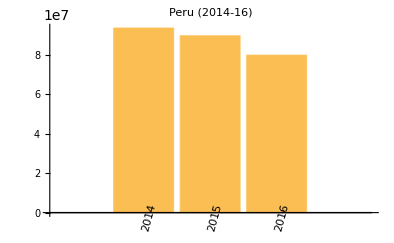

Figure 4 consists of three charts which provide the total amount of money donated to Jordan, Ethiopia and Peru in the range of years 2014-2016. By looking at these charts we can see three different trends during the range of years under investigation. With time an increase and a decrease is visible for Jordan. Moreover, an increase for Ethiopia and a decrease for Peru are also visible.

Mathematica notebook: ProjectWSS2017_Dradi2.nb

Code

Provide one of:

Link to the GitHub

Explicit code

Written Content / Lesson Plans

Conclusions in Detail

Fluctuations in the U.S. foreign assistance spending are clearly visible in our results. Our analysis is able to show the different contributions of the several U.S. agencies to the studied categories of any country of the sample.

All Visualizations

Data Sources Links/References

The database of Peru 2016 has been imported from the website “http://foreignassistance.gov” by using the following API code:

```mathematica
dataPeru2016=URLExecute["http://fagov-api-prod.azurewebsites.net/api/public/activities",{"format"->"json","fundingType"->"obligated","filterType"->"location","filterValue"->"peru","year"->"2016"},"RawJSON"];
```

The database of the sample of countries “listCountrySample” under investigation has instead been imported by using the following API code:

```mathematica
datasetsCS=Cases[Map[#-> URLExecute["http://fagov-api-prod.azurewebsites.net/api/public/activities",{"format"->"json","fundingType"->"obligated","filterType"->"location","filterValue"->#,"year"->"2016"},"RawJSON"]&,listCountrySample], _[_, _List]];
```

Notice that the function Cases with “_[ _, _List]”  gives a list of elements which have the structure “_[ _, _List]”. Therefore, such a line removes from the total dataset, the dataset of countries which do not have any data.

Future Directions

Possible connections between international presidential trips made by Barack Obama and our data would be an interesting topic to be studied. If we had had more time, we would have probably concentrated more carefully on the  data concerning Ethiopia first of all. After President Obama became the first sitting U.S. president to travel to Ethiopia in July  2015, we can see an increase of U.S. government’s commitment towards Ethiopia.

Background Info Links/References

For further information, please consult the following website: http://foreignassistance.gov

Keywords

U.S. Government Foreign Assistance

Data analysis

Central repository “ForeignAssistance.gov”

Other

Mathematica notebook: 
ProjectWSS2017_Dradi1.nb 
ProjectWSS2017_Dradi2.nb 
ProjectWSS2017_Dradi3.nb 

Note that you can run the notebooks “ProjectWSS2017_Dradi2.nb” and “ProjectWSS2017_Dradi3.nb” only if you import the following mx files: 
- aGENCY2013.mx, aGENCY2014.mx, aGENCY2015.mx, aGENCY2016.mx
- categorieS2013.mx, categorieS2014.mx, categorieS2015.mx, categorieS2016.mx
- datasets2013.mx, datasets2014.mx, datasets2015.mx, datasets2016.mx

Our sample of countries: 

Jordan,Algeria,Angola,Argentina,Armenia,Austria,China,Croatia,Estonia,Ethiopia,Georgia,Kenya,Latvia,Libya,Namibia,Russia,Somalia,Uganda,Antarctica,Bulgaria,Liberia,Luxembourg,Slovakia,Taiwan,Chile,Ireland,Portugal,Australia,Israel,Niger,Venezuela,Cuba,Ecuador,Guatemala,Honduras,Mexico,Peru,Afghanistan,Albania,Andorra,Anguilla,Aruba,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Botswana,Brazil,Brunei,Burundi,Cambodia,Cameroon,Canada,Chad,Colombia,Comoros,Cyprus,Denmark,Djibouti,Dominica,Egypt,Eritrea,Fiji,Finland,France,Gabon,Gambia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guernsey,Guinea,Guyana,Haiti,Hungary,Iceland,India,Indonesia,Iran,Iraq,Italy,Jamaica,Japan,Jersey,Kazakhstan,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Lebanon,Lesotho,Liechtenstein,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Martinique,Mauritania,Mauritius,Mayotte,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Nauru,Nepal,Netherlands,Nicaragua,Nigeria,Niue,Norway,Oman,Pakistan,Palau,Panama,Paraguay,Philippines,Poland,Qatar,Réunion,Romania,Rwanda,Samoa,Senegal,Serbia,Seychelles,Singapore,Slovenia,Spain,Sudan,Suriname,Swaziland,Sweden,Switzerland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Tunisia,Turkey,Turkmenistan,Tuvalu,Ukraine,Uruguay,Uzbekistan,Vanuatu,Vietnam,Yemen,Zambia,Zimbabwe,Macau,Svalbard,Curacao. 

Agencies: 

Department of Agriculture
Department of Commerce
Department of Defense
Department of Energy
Department of Health and Human Services
Department of Homeland Security
Department of the Interior
Department of Justice
Department of Labor
Department of State
Department of the Treasury
Department of Transportation
Environmental Protection Agency
Federal Trade Commission
Inter-American Foundation
Millennium Challenge Corporation
Peace Corps
U.S. African Development Foundation
U.S. Agency for International Development
U.S. Trade Development Agency

Categories: 

Multi-sector
Program Management
Health
Humanitarian Assistance 
Economic Development
Democracy, Human Rights, and Governace
Education and Social Services
Peace and Security
"

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```